### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 130,I2->128, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming(*does not get all us in the first "step"*)
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

u1≥u30&&u32≤u2&&u16≤u21&&u18≤u25&&u20≤u27

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

{u1,u29,u31}{u29,u31}{u1,u29,u31}{u1,u29,u31}

{u29,u31}{u31}{u1}{}

{u31}{}{u1}{}

{}{}{u1}{}

(Maybe the) system is not feasible!

            	Check the paper: The current method for stationary mean-field games on networks

{0.155751,Null}

```mathematica
{0.173389,<|u1->16529/41,u2->20494/41,u3->16529/41,u4->12523/41,u5->20494/41,u6->13799/41,u7->12523/41,u8->13799/41,u9->12523/41,u10->7241/41,u11->13799/41,u12->8380/41,u13->7241/41,u14->8380/41,u15->7241/41,u16->20,u17->8380/41,u18->100,u19->20,u20->0,u21->20,u22->20,u23->100,u24->0,u25->100,u26->100,u27->0,u28->0,u29->16529/41,u30->16529/41,u31->20494/41,u32->20494/41,j21->0,j22->5601/41,j25->0,j26->180/41,j27->0,j28->120,j29->0,j30->1,j31->0,j32->260,j12->5419/41,j14->0,j16->6421/41,j18->4280/41,j2->0,j20->20,j24->100,j4->4006/41,j6->6695/41,j8->0,j9->0,j1->3965/41,j10->5282/41,j11->0,j13->1139/41,j15->0,j17->0,j19->0,j23->0,j3->0,j5->0,j7->1276/41|>}//N
```

{0.173389,<|u1→403.146,u2→499.854,u3→403.146,u4→305.439,u5→499.854,u6→336.561,u7→305.439,u8→336.561,u9→305.439,u10→176.61,u11→336.561,u12→204.39,u13→176.61,u14→204.39,u15→176.61,u16→20.,u17→204.39,u18→100.,u19→20.,u20→0.,u21→20.,u22→20.,u23→100.,u24→0.,u25→100.,u26→100.,u27→0.,u28→0.,u29→403.146,u30→403.146,u31→499.854,u32→499.854,j21→0.,j22→136.61,j25→0.,j26→4.39024,j27→0.,j28→120.,j29→0.,j30→1.,j31→0.,j32→260.,j12→132.171,j14→0.,j16→156.61,j18→104.39,j2→0.,j20→20.,j24→100.,j4→97.7073,j6→163.293,j8→0.,j9→0.,j1→96.7073,j10→128.829,j11→0.,j13→27.7805,j15→0.,j17→0.,j19→0.,j23→0.,j3→0.,j5→0.,j7→31.122|>}

```mathematica
Reduce[u1≥u29&&u31≤40+jt14/4+jt16/4-jt17/4-jt18/4+u1&&220-5 jt14-5 jt16+5 jt17+5 jt18+u1≤20&&-840+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1≤100&&-1340+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1≤0&&(60-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20==0||u1-u29==0)&&(-40+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20==0||u1-u29==0)&&(200-jt12==0||40+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt12==0||40+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt14+jt16-jt25+jt28-jt37==0||-200+5 jt14+5 jt16-5 jt17-5 jt18-u1==0)&&(-1840+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46==0||-200+5 jt14+5 jt16-5 jt17-5 jt18-u1==0)&&(jt32+jt34-jt43==0||940-(21 jt14)/4-(21 jt16)/4+(21 jt17)/4+(21 jt18)/4-u1==0)&&(jt46==0||940-(21 jt14)/4-(21 jt16)/4+(21 jt17)/4+(21 jt18)/4-u1==0)&&(500-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46==0||1340-9 jt14-9 jt16+9 jt17+9 jt18-jt32-jt34+jt43-jt46-u1==0)&&(1560-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46==0||1340-9 jt14-9 jt16+9 jt17+9 jt18-jt32-jt34+jt43-jt46-u1==0)&&u1≥u29&&(60-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20==0||u1-u29==0)&&(-40+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20==0||u1-u29==0)&&u31≤40+jt14/4+jt16/4-jt17/4-jt18/4+u1&&(200-jt12==0||40+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt12==0||40+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)]
```

((jt16|jt17|jt18|jt34|jt43|jt46)∈ℝ&&u29==14600/41&&u31==1/4 (64960/41+jt16-jt17-jt18+1/5 (22800/41-5 jt16+5 jt17+5 jt18))&&u1==14600/41&&jt32==1340-9 jt16+9 jt17+9 jt18-jt34+jt43-jt46-u1-9/5 (200-5 jt16+5 jt17+5 jt18+u1)&&jt14==1/5 (200-5 jt16+5 jt17+5 jt18+u1))||((jt16|jt17|jt18|jt34|jt43)∈ℝ&&u29==350&&u31==1/4 (1560+jt16-jt17-jt18+1/5 (550-5 jt16+5 jt17+5 jt18))&&u1==350&&jt46==0&&jt32==-jt34+jt43&&jt14==1/5 (200-5 jt16+5 jt17+5 jt18+u1))

```mathematica
Reduce[%,Reals]
```

(u31==17380/41&&u29==14600/41&&u1==14600/41&&jt32==-700/41-jt34+jt43-jt46&&jt14==4560/41-jt16+jt17+jt18)||(u31==835/2&&u29==350&&u1==350&&jt46==0&&jt32==-jt34+jt43&&jt14==110-jt16+jt17+jt18)

```mathematica
u1≥u29&&u31≤499+jt14/4+jt16/4-jt17/4-jt18/4+u1&&2002-5 jt14-5 jt16+5 jt17+5 jt18+u1≤20&&-7509+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1≤100&&-12014+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1≤0&&(501-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20==0||u1-u29==0)&&(-499+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20==0||u1-u29==0)&&(2000-jt12==0||499+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt12==0||499+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt14+jt16-jt25+jt28-jt37==0||-1982+5 jt14+5 jt16-5 jt17-5 jt18-u1==0)&&(-16519+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46==0||-1982+5 jt14+5 jt16-5 jt17-5 jt18-u1==0)&&(jt32+jt34-jt43==0||7609-(21 jt14)/4-(21 jt16)/4+(21 jt17)/4+(21 jt18)/4-u1==0)&&(jt46==0||7609-(21 jt14)/4-(21 jt16)/4+(21 jt17)/4+(21 jt18)/4-u1==0)&&(4505-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46==0||12014-9 jt14-9 jt16+9 jt17+9 jt18-jt32-jt34+jt43-jt46-u1==0)&&(14016-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46==0||12014-9 jt14-9 jt16+9 jt17+9 jt18-jt32-jt34+jt43-jt46-u1==0)&&u1≥u29&&(501-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20==0||u1-u29==0)&&(-499+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20==0||u1-u29==0)&&u31≤499+jt14/4+jt16/4-jt17/4-jt18/4+u1&&(2000-jt12==0||499+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt12==0||499+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)//Reduce//Reduce[#,Reals]&
```

u29==110558/41&&u31==140608/41&&u1==110558/41&&jt32==36740/41-jt34+jt43-jt46&&jt14==38364/41-jt16+jt17+jt18

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 2,I2->2000, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

u1≥u30&&u32≤u2&&u16≤u21&&u18≤u25&&u20≤u27

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.148422,<|u1→110558/41,u2→140608/41,u3→110558/41,u4→80426/41,u5→140608/41,u6→88658/41,u7→80426/41,u8→88658/41,u9→80426/41,u10→42062/41,u11→88658/41,u12→44940/41,u13→42062/41,u14→44940/41,u15→42062/41,u16→20,u17→44940/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→110558/41,u30→110558/41,u31→140608/41,u32→140608/41,j1→30050/41,j2→0,j3→0,j4→30132/41,j5→0,j6→51950/41,j7→8232/41,j8→0,j9→0,j10→38364/41,j11→0,j12→43718/41,j13→2878/41,j14→0,j15→0,j16→41242/41,j17→0,j18→40840/41,j19→0,j20→20,j21→0,j22→40422/41,j23→0,j24→100,j25→0,j26→36740/41,j27→0,j28→120,j29→0,j30→2,j31→0,j32→2000|>}

```mathematica
CriticalCongestionSolver2[d2e]//AbsoluteTiming
```

EliminateVarsSimplify for the us

all variables at the same time!

Finished with the us!

Finish with the js

all variables at the same time!

{0.07423,<|u1→110558/41,u2→140608/41,u3→110558/41,u4→80426/41,u5→140608/41,u6→88658/41,u7→80426/41,u8→88658/41,u9→80426/41,u10→42062/41,u11→88658/41,u12→44940/41,u13→42062/41,u14→44940/41,u15→42062/41,u16→20,u17→44940/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→110558/41,u30→110558/41,u31→140608/41,u32→140608/41,j21→0,j22→40422/41,j25→0,j26→36740/41,j27→0,j28→120,j29→0,j30→2,j31→0,j32→2000,j12→43718/41,j14→0,j16→41242/41,j18→40840/41,j2→0,j20→20,j24→100,j4→30132/41,j6→51950/41,j8→0,j9→0,j1→30050/41,j10→38364/41,j11→0,j13→2878/41,j15→0,j17→0,j19→0,j23→0,j3→0,j5→0,j7→8232/41|>}

```mathematica
Select[jt14+jt16+4 (4+jt19+jt20)≥4 jt12+jt17+jt18&&jt19+jt20≥jt12&&4 jt13+3 jt14+jt17+jt18≥24+jt16&&jt13+jt14≥0&&jt14+jt16+4 (jt19+jt20)≥64+jt17+jt18&&jt19+jt20≥0&&4 jt13+3 jt14+3 jt16+jt18≥3 (8+jt17)&&jt13+jt18≥0&&jt17+jt18≥0&&jt14+jt16≥0&&jt14+jt16+jt20+jt22≥22+jt17+jt18&&jt20+jt22≥0&&jt17+jt18+jt28≥jt29&&112+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt29&&112+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt25&&jt14+jt16+jt28≥jt25&&15 jt14+15 jt16+4 (jt32+jt34)≥5 (40+3 jt17+3 jt18)&&jt32+jt34≥0&&14 jt14+14 jt16+jt32+jt34+jt37+jt46≥156+14 jt17+14 jt18+jt43&&jt37≥0&&71 jt14+71 jt16+4 (jt32+jt34+jt46)≥736+71 jt17+71 jt18+4 jt43&&(15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46≥5/4 (40+3 jt17+3 jt18)&&jt43≥0&&jt32+jt34+jt46≥jt43&&824+71 jt17+71 jt18+8 jt43≥71 jt14+71 jt16+8 (jt32+jt34+jt46)&&jt14+jt16+4 (4+jt19+jt20)≥4 jt12+jt17+jt18&&4 jt13+3 jt14+jt17+jt18≥24+jt16&&jt16+4 (6+jt19+jt20)≥4 jt12+4 jt13+3 jt14+jt17+jt18&&4 jt12+4 jt13+3 jt14+jt17+jt18≥jt16+4 (4+jt19+jt20)&&jt19+jt20≥jt12&&jt14+jt16+4 (jt19+jt20)≥64+jt17+jt18&&jt12≤20&&jt12≥0&&jt13≥0&&jt14≥0&&4 jt13+3 jt14+jt18≥24+jt16+3 jt17&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt13+jt18≥jt22&&jt22≥0&&jt14+jt16+4 (jt19+jt20+jt22)≥64+4 jt13+jt17+5 jt18&&4 jt13+3 jt14+3 jt16+jt18≥24+3 jt17+4 jt19&&jt25≥0&&jt14+jt16≥jt25&&jt17+jt18≥jt29&&jt28≥0&&jt29≥0&&15 jt17+15 jt18+4 (28+jt28)≥11 jt14+11 jt16+4 (jt25+jt29)&&jt20+jt22≥jt32&&jt32≥0&&15 jt17+15 jt18+4 (28+jt28)≥11 jt14+11 jt16+4 (jt29+jt34)&&jt34≥0&&(15 jt14)/4+(15 jt16)/4+jt20+jt22+jt29+jt34≥50+(19 jt17)/4+(19 jt18)/4+jt28&&jt17+jt18+jt28+jt32≥jt20+jt22+jt29&&jt37≥0&&jt14+jt16+jt28≥jt25+jt37&&112+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt25&&(67 jt14)/4+(67 jt16)/4+jt25+jt32+jt34+jt37+jt46≥184+(71 jt17)/4+(71 jt18)/4+jt28+jt43&&jt43≥0&&jt32+jt34≥jt43&&15 jt14+15 jt16+4 (jt32+jt34)≥5 (40+3 jt17+3 jt18)&&jt46≥0&&(15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46≥5/4 (40+3 jt17+3 jt18)&&15 jt17+15 jt18+4 (50+jt37)≥15 jt14+15 jt16+4 (jt32+jt34+jt46)&&14 jt14+14 jt16+jt32+jt34+jt37+jt46≥156+14 jt17+14 jt18+jt43&&2 (78+7 jt17+7 jt18+jt43)≥14 jt14+14 jt16+jt32+jt34+jt37+jt46&&u1≥u1&&2+5 jt17+5 jt18+u1≤5 (jt14+jt16)&&21 jt14+21 jt16+4 u1≤736+21 jt17+21 jt18&&9 jt14+9 jt16+jt32+jt34+jt46+u1≤134+9 jt17+9 jt18+jt43&&(4 jt12+jt17+jt18==jt14+jt16+4 (4+jt19+jt20)||jt12==jt19+jt20)&&(4 jt13+3 jt14+jt17+jt18==24+jt16||jt13+jt14==0)&&(jt14+jt16+4 (jt19+jt20)==64+jt17+jt18||jt19+jt20==0)&&(4 jt13+3 jt14+3 jt16+jt18==3 (8+jt17)||jt13+jt18==0)&&(jt17+jt18==0||jt14+jt16==0)&&(jt14+jt16+jt20+jt22==22+jt17+jt18||jt20+jt22==0)&&(jt17+jt18+jt28==jt29||11 jt14+11 jt16+4 jt29==112+15 jt17+15 jt18+4 jt28)&&(11 jt14+11 jt16+4 jt25==112+15 jt17+15 jt18+4 jt28||jt14+jt16+jt28==jt25)&&(15 jt14+15 jt16+4 (jt32+jt34)==5 (40+3 jt17+3 jt18)||jt32+jt34==0)&&(14 jt14+14 jt16+jt32+jt34+jt37+jt46==156+14 jt17+14 jt18+jt43||jt37==0)&&((15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46==5/4 (40+3 jt17+3 jt18)||jt43==0)&&(4 jt12+jt17+jt18==jt14+jt16+4 (4+jt19+jt20)||4 jt13+3 jt14+jt17+jt18==24+jt16)&&(jt13==0||4 jt13+3 jt14+jt18==24+jt16+3 jt17)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt13+jt18==jt22)&&(jt20==0||64+4 jt13+jt17+5 jt18==jt14+jt16+4 (jt19+jt20+jt22))&&(jt22==0||4 jt13+3 jt14+3 jt16+jt18==24+3 jt17+4 jt19)&&(jt25==0||jt17+jt18==jt29)&&(jt14+jt16==jt25||jt29==0)&&(jt28==0||11 jt14+11 jt16+4 (jt25+jt29)==15 jt17+15 jt18+4 (28+jt28))&&(jt20+jt22==jt32||11 jt14+11 jt16+4 (jt29+jt34)==15 jt17+15 jt18+4 (28+jt28))&&(jt32==0||(15 jt14)/4+(15 jt16)/4+jt20+jt22+jt29+jt34==50+(19 jt17)/4+(19 jt18)/4+jt28)&&(jt34==0||jt17+jt18+jt28+jt32==jt20+jt22+jt29)&&(jt37==0||11 jt14+11 jt16+4 jt25==112+15 jt17+15 jt18+4 jt28)&&(jt43==0||15 jt14+15 jt16+4 (jt32+jt34)==5 (40+3 jt17+3 jt18))&&((15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46==5/4 (40+3 jt17+3 jt18)||14 jt14+14 jt16+jt32+jt34+jt37+jt46==156+14 jt17+14 jt18+jt43)&&(jt12==jt19+jt20||jt14+jt16+4 (jt19+jt20)==64+jt17+jt18)&&(jt14+jt16+jt28==jt25+jt37||5 (jt14+jt16)==2+5 jt17+5 jt18+u1)&&((67 jt14)/4+(67 jt16)/4+jt25+jt32+jt34+jt37+jt46==184+(71 jt17)/4+(71 jt18)/4+jt28+jt43||5 (jt14+jt16)==2+5 jt17+5 jt18+u1)&&(jt32+jt34==jt43||21 jt14+21 jt16+4 u1==736+21 jt17+21 jt18)&&(jt46==0||21 jt14+21 jt16+4 u1==736+21 jt17+21 jt18)&&(15 jt14+15 jt16+4 (jt32+jt34+jt46)==15 jt17+15 jt18+4 (50+jt37)||9 jt14+9 jt16+jt32+jt34+jt46+u1==134+9 jt17+9 jt18+jt43)&&(2 (78+7 jt17+7 jt18+jt43)==14 jt14+14 jt16+jt32+jt34+jt37+jt46||9 jt14+9 jt16+jt32+jt34+jt46+u1==134+9 jt17+9 jt18+jt43),Function[exp, !FreeQ[exp,jt14]
]]
```

```mathematica
jt14+jt16+4 (4+jt19+jt20)≥4 jt12+jt17+jt18&&4 jt13+3 jt14+jt17+jt18≥24+jt16&&jt13+jt14≥0&&jt14+jt16+4 (jt19+jt20)≥64+jt17+jt18&&4 jt13+3 jt14+3 jt16+jt18≥3 (8+jt17)&&jt14+jt16≥0&&jt14+jt16+jt20+jt22≥22+jt17+jt18&&112+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt29&&112+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt25&&jt14+jt16+jt28≥jt25&&15 jt14+15 jt16+4 (jt32+jt34)≥5 (40+3 jt17+3 jt18)&&14 jt14+14 jt16+jt32+jt34+jt37+jt46≥156+14 jt17+14 jt18+jt43&&71 jt14+71 jt16+4 (jt32+jt34+jt46)≥736+71 jt17+71 jt18+4 jt43&&(15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46≥5/4 (40+3 jt17+3 jt18)&&824+71 jt17+71 jt18+8 jt43≥71 jt14+71 jt16+8 (jt32+jt34+jt46)&&jt14+jt16+4 (4+jt19+jt20)≥4 jt12+jt17+jt18&&4 jt13+3 jt14+jt17+jt18≥24+jt16&&jt16+4 (6+jt19+jt20)≥4 jt12+4 jt13+3 jt14+jt17+jt18&&4 jt12+4 jt13+3 jt14+jt17+jt18≥jt16+4 (4+jt19+jt20)&&jt14+jt16+4 (jt19+jt20)≥64+jt17+jt18&&jt14≥0&&4 jt13+3 jt14+jt18≥24+jt16+3 jt17&&jt14+jt16+4 (jt19+jt20+jt22)≥64+4 jt13+jt17+5 jt18&&4 jt13+3 jt14+3 jt16+jt18≥24+3 jt17+4 jt19&&jt14+jt16≥jt25&&15 jt17+15 jt18+4 (28+jt28)≥11 jt14+11 jt16+4 (jt25+jt29)&&15 jt17+15 jt18+4 (28+jt28)≥11 jt14+11 jt16+4 (jt29+jt34)&&(15 jt14)/4+(15 jt16)/4+jt20+jt22+jt29+jt34≥50+(19 jt17)/4+(19 jt18)/4+jt28&&jt14+jt16+jt28≥jt25+jt37&&112+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt25&&(67 jt14)/4+(67 jt16)/4+jt25+jt32+jt34+jt37+jt46≥184+(71 jt17)/4+(71 jt18)/4+jt28+jt43&&15 jt14+15 jt16+4 (jt32+jt34)≥5 (40+3 jt17+3 jt18)&&(15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46≥5/4 (40+3 jt17+3 jt18)&&15 jt17+15 jt18+4 (50+jt37)≥15 jt14+15 jt16+4 (jt32+jt34+jt46)&&14 jt14+14 jt16+jt32+jt34+jt37+jt46≥156+14 jt17+14 jt18+jt43&&2 (78+7 jt17+7 jt18+jt43)≥14 jt14+14 jt16+jt32+jt34+jt37+jt46&&2+5 jt17+5 jt18+u1≤5 (jt14+jt16)&&21 jt14+21 jt16+4 u1≤736+21 jt17+21 jt18&&9 jt14+9 jt16+jt32+jt34+jt46+u1≤134+9 jt17+9 jt18+jt43&&(4 jt12+jt17+jt18==jt14+jt16+4 (4+jt19+jt20)||jt12==jt19+jt20)&&(4 jt13+3 jt14+jt17+jt18==24+jt16||jt13+jt14==0)&&(jt14+jt16+4 (jt19+jt20)==64+jt17+jt18||jt19+jt20==0)&&(4 jt13+3 jt14+3 jt16+jt18==3 (8+jt17)||jt13+jt18==0)&&(jt17+jt18==0||jt14+jt16==0)&&(jt14+jt16+jt20+jt22==22+jt17+jt18||jt20+jt22==0)&&(jt17+jt18+jt28==jt29||11 jt14+11 jt16+4 jt29==112+15 jt17+15 jt18+4 jt28)&&(11 jt14+11 jt16+4 jt25==112+15 jt17+15 jt18+4 jt28||jt14+jt16+jt28==jt25)&&(15 jt14+15 jt16+4 (jt32+jt34)==5 (40+3 jt17+3 jt18)||jt32+jt34==0)&&(14 jt14+14 jt16+jt32+jt34+jt37+jt46==156+14 jt17+14 jt18+jt43||jt37==0)&&((15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46==5/4 (40+3 jt17+3 jt18)||jt43==0)&&(4 jt12+jt17+jt18==jt14+jt16+4 (4+jt19+jt20)||4 jt13+3 jt14+jt17+jt18==24+jt16)&&(jt13==0||4 jt13+3 jt14+jt18==24+jt16+3 jt17)&&(jt14==0||jt17==0)&&(jt20==0||64+4 jt13+jt17+5 jt18==jt14+jt16+4 (jt19+jt20+jt22))&&(jt22==0||4 jt13+3 jt14+3 jt16+jt18==24+3 jt17+4 jt19)&&(jt14+jt16==jt25||jt29==0)&&(jt28==0||11 jt14+11 jt16+4 (jt25+jt29)==15 jt17+15 jt18+4 (28+jt28))&&(jt20+jt22==jt32||11 jt14+11 jt16+4 (jt29+jt34)==15 jt17+15 jt18+4 (28+jt28))&&(jt32==0||(15 jt14)/4+(15 jt16)/4+jt20+jt22+jt29+jt34==50+(19 jt17)/4+(19 jt18)/4+jt28)&&(jt37==0||11 jt14+11 jt16+4 jt25==112+15 jt17+15 jt18+4 jt28)&&(jt43==0||15 jt14+15 jt16+4 (jt32+jt34)==5 (40+3 jt17+3 jt18))&&((15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46==5/4 (40+3 jt17+3 jt18)||14 jt14+14 jt16+jt32+jt34+jt37+jt46==156+14 jt17+14 jt18+jt43)&&(jt12==jt19+jt20||jt14+jt16+4 (jt19+jt20)==64+jt17+jt18)&&(jt14+jt16+jt28==jt25+jt37||5 (jt14+jt16)==2+5 jt17+5 jt18+u1)&&((67 jt14)/4+(67 jt16)/4+jt25+jt32+jt34+jt37+jt46==184+(71 jt17)/4+(71 jt18)/4+jt28+jt43||5 (jt14+jt16)==2+5 jt17+5 jt18+u1)&&(jt32+jt34==jt43||21 jt14+21 jt16+4 u1==736+21 jt17+21 jt18)&&(jt46==0||21 jt14+21 jt16+4 u1==736+21 jt17+21 jt18)&&(15 jt14+15 jt16+4 (jt32+jt34+jt46)==15 jt17+15 jt18+4 (50+jt37)||9 jt14+9 jt16+jt32+jt34+jt46+u1==134+9 jt17+9 jt18+jt43)&&(2 (78+7 jt17+7 jt18+jt43)==14 jt14+14 jt16+jt32+jt34+jt37+jt46||9 jt14+9 jt16+jt32+jt34+jt46+u1==134+9 jt17+9 jt18+jt43)//Reduce
```

$Aborted

```mathematica
us/.rule
```

{110558/41,140608/41,110558/41,80426/41,140608/41,88658/41,80426/41,88658/41,80426/41,42062/41,88658/41,44940/41,42062/41,44940/41,42062/41,20,44940/41,100,20,0,20,20,100,0,100,100,0,0,110558/41,110558/41,140608/41,140608/41}

```mathematica
js/.rule
```

{30050/41,0,0,30132/41,0,51950/41,8232/41,0,0,38364/41,0,43718/41,2878/41,0,0,41242/41,0,40840/41,0,20,0,40422/41,0,100,0,36740/41,0,120,0,2,0,2000}

```mathematica
(rule1=CriticalCongestionSolverNewReduce[d2e=D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

present vars: {u1,u29,u31,jt14,jt16,jt17,jt18,jt32,jt34,jt43,jt46,jt12,jt13,jt19,jt20,jt25,jt28,jt37}

Finished with the us!

Finish with the js

present vars: {j1}

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47522,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47522,Head[#1]===Or&]} generated message(s) {Select::normal}.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47532,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47532,Head[#1]===Or&]} generated message(s) {Select::normal}.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47546,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47546,Head[#1]===Or&]} generated message(s) {Select::normal}.

General::stop: Further output of Exists::msgs will be suppressed during this calculation.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

present vars: {}

present vars: {j11}

present vars: {}

present vars: {}

present vars: {}

«2 more identical outputs»

{0.408283,<|u1→10807580/41,u2→13807180/41,u3→10807580/41,u4→7807160/41,u5→13807180/41,u6→8606780/41,u7→7807160/41,u8→8606780/41,u9→7807160/41,u10→4007120/41,u11→8606780/41,u12→4206000/41,u13→4007120/41,u14→4206000/41,u15→4007120/41,u16→200,u17→4206000/41,u18→100,u19→200,u20→0,u21→200,u22→200,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→10807580/41,u30→10807580/41,u31→13807180/41,u32→13807180/41,j21→0,j22→3990720/41,j25→0,j26→4197800/41,j27→0,j28→300,j29→0,j30→20,j31→0,j32→200000,j12→4400780/41,j14→-198880/41+j13,j16→3998920/41+j15,j18→4201900/41+j17,j2→0,j20→200+j19,j24→100+j23,j4→3000420/41+j3,j6→5200400/41+j5,j8→-799620/41+j7,j9→-3800040/41+j10,j1→2999600/41,j11→0|>}

```mathematica
uvars=d2e["uvars"];
us=Values@uvars;
jvars=d2e["jvars"];
js=Values@jvars;
jtvars=d2e["jtvars"];
jts=Values@jtvars;
```

### Quest for subsystems!

#### how to find variables in some expressions of the system

```mathematica
getVar::usage ="getVar[exp] returns the variables in exp"
getVar[xp_And]:=getVar/@List@@xp//Flatten//DeleteDuplicates
getVar[GreaterEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[Equal[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[LessEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[xp_Or]:=getVar/@List@@xp//Flatten
```

```mathematica
colapse[{xp1_,xp2_}]:=
Which[SubsetQ[xp1,xp2],
xp1,
SubsetQ[xp2,xp1] ,
xp2,
True,
{xp1,xp2}
]
```

```mathematica
SimpleCrit[{{True,rules_}, critus_}]:={{True,rules},critus}
SimpleCrit[{{syscrit_,rules_},{}}]:=
Module[{subsol, newcrit= Simplify/@syscrit},
subsol = First@Solve[newcrit];
{{newcrit/.subsol,Join[rules,Association[subsol]]/.subsol}, {}}
]

SimpleCrit[{{syscrit_,rules_},critus_}]:=
Module[{var,subsys,subsol, newcrit = Simplify/@syscrit},
var=First[critus];
subsys=Select[newcrit, Function[xp, !FreeQ[var][xp]]];
If[subsys===True,
Return[{{newcrit,rules}, Rest[critus]}]
];
subsol=First@Solve[subsys[[1]],var];
{{syscrit/.subsol,Join[rules,Association[subsol]]/.subsol},Rest[critus]}
]
```

### got to fix the “got And”!!

```mathematica
EliminateVars2[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep2,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep2[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
(*subsys=Simplify[subsys];*)
subsys=Reduce[subsys,Reals];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualitiesOperator[d2e][{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
us/.(Expand/@rules)
```

{10807580/41,13807180/41,10807580/41,7807160/41,13807180/41,8606780/41,7807160/41,8606780/41,7807160/41,4007120/41,8606780/41,4206000/41,4007120/41,4206000/41,4007120/41,200,4206000/41,100,200,0,200,200,100,0,100,100,0,0,10807580/41,10807580/41,13807180/41,13807180/41}

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rules]
```

ReplaceAll::reps: {rules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeyMap::invak: The argument <|{1,1->2}→u1,{2,1->2}→u2,{1,1->3}→u3,{3,1->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->4}→u7,{4,3->4}→u8,{3,3->5}→u9,{5,3->5}→u10,{4,4->6}→u11,{6,4->6}→u12,{5,5->6}→u13,{6,5->6}→u14,{5,5->7}→u15,{7,5->7}→u16,{6,6->8}→u17,{8,6->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->ex7}→u21,{ex7,7->ex7}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->ex8}→u25,{ex8,8->ex8}→u26,{9,9->ex9}→u27,{ex9,9->ex9}→u28,{en1,en1->1}→u29,{1,en1->1}→u30,{en2,en2->2}→u31,{2,en2->2}→u32|>/.rules is not a valid Association.

ReplaceAll::reps: {KeyMap[#1⟦1⟧&,<|{1,1->2}→u1,{2,1->2}→u2,{1,1->3}→u3,{3,1->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->4}→u7,{4,3->4}→u8,{3,3->5}→u9,{5,3->5}→u10,{4,4->6}→u11,{6,4->6}→u12,{5,5->6}→u13,{6,5->6}→u14,{5,5->7}→u15,{7,5->7}→u16,{6,6->8}→u17,{8,6->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->ex7}→u21,{ex7,7->ex7}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->ex8}→u25,{ex8,8->ex8}→u26,{9,9->ex9}→u27,{ex9,9->ex9}→u28,{en1,en1->1}→u29,{1,en1->1}→u30,{en2,en2->2}→u31,{2,en2->2}→u32|>/.rules]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

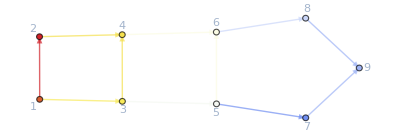

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

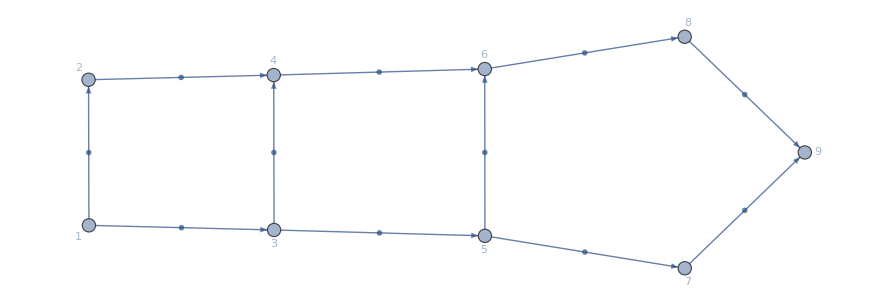

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

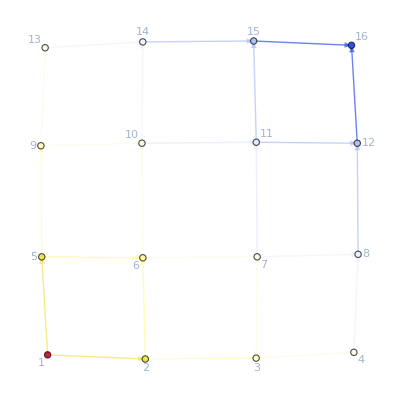

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Solve//FindInstance
```

FindInstance[{{jt28→ConditionalExpression[1/7 (6-7 jt31), 0≤jt31≤6/7],jt40→ConditionalExpression[1/7 (4-7 jt43), 0≤jt43≤4/7],jt64→ConditionalExpression[1/7 (6-7 jt67), 0≤jt67≤4/7],jt76→ConditionalExpression[1/7 (6-7 jt79), 0≤jt79≤6/7]}}]

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,1000,10}]
```

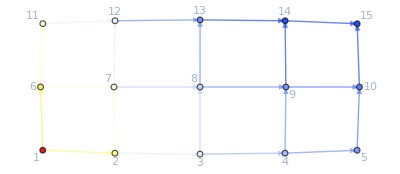

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

# TestZone

#### This is the winning code! Try this on CriticalCongestionSolverNewReduce

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

```mathematica
Kirch=j1==jt1+jt2&&j3==jt3+jt4&&j30==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j32==jt11+jt12&&j4==jt13+jt14&&j7==jt15+jt16&&j9==jt17+jt18&&j6==jt19+jt20&&j8==jt21+jt22&&j11==jt23+jt24&&j10==jt25+jt26&&j13==jt27+jt28&&j15==jt29+jt30&&j12==jt31+jt32&&j14==jt33+jt34&&j17==jt35+jt36&&j16==jt37+jt38&&j19==jt39+jt40&&j21==jt41+jt42&&j18==jt43+jt44&&j23==jt45+jt46&&j25==jt47+jt48&&j20==jt49+jt50&&j24==jt51+jt52&&j27==jt53+jt54&&j2==jt3+jt5&&j4==jt1+jt6&&j29==jt2+jt4&&j1==jt11+jt9&&j6==jt12+jt7&&j31==jt10+jt8&&j3==jt15+jt17&&j8==jt13+jt18&&j10==jt14+jt16&&j5==jt21+jt23&&j7==jt19+jt24&&j12==jt20+jt22&&j9==jt27+jt29&&j14==jt25+jt30&&j16==jt26+jt28&&j11==jt33+jt35&&j13==jt31+jt36&&j18==jt32+jt34&&j15==jt39+jt41&&j20==jt37+jt42&&j22==jt38+jt40&&j17==jt45+jt47&&j24==jt43+jt48&&j26==jt44+jt46&&j19==jt51+jt53&&j23==jt49+jt54&&j28==jt50+jt52;
```

```mathematica
getVar[Kirch]
```

{j1,jt1,jt2,j3,jt3,jt4,j30,jt5,jt6,j2,jt7,jt8,j5,jt10,jt9,j32,jt11,jt12,j4,jt13,jt14,j7,jt15,jt16,j9,jt17,jt18,j6,jt19,jt20,j8,jt21,jt22,j11,jt23,jt24,j10,jt25,jt26,j13,jt27,jt28,j15,jt29,jt30,j12,jt31,jt32,j14,jt33,jt34,j17,jt35,jt36,j16,jt37,jt38,j19,jt39,jt40,j21,jt41,jt42,j18,jt43,jt44,j23,jt45,jt46,j25,jt47,jt48,j20,jt49,jt50,j24,jt51,jt52,j27,jt53,jt54,j29,j31,j22,j26,j28}

```mathematica
js=Values@d2e["jvars"];
```

```mathematica
Intersection[js, getVar[Kirch]]//Sort
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j3,j30,j31,j32,j4,j5,j6,j7,j8,j9}

```mathematica
js//Sort
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j3,j30,j31,j32,j4,j5,j6,j7,j8,j9}

```mathematica
Solve[Kirch, js]
```

{}

```mathematica
Length[Kirch]
```

54

```mathematica
Length[js]
```

32

```mathematica
d2e["EqTransitionCompCon"]
```

(jt1==0||jt3==0)&&(jt10==0||jt12==0)&&(jt11==0||jt8==0)&&(jt13==0||jt15==0)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt21==0)&&(jt2==0||jt5==0)&&(jt20==0||jt23==0)&&(jt22==0||jt24==0)&&(jt25==0||jt27==0)&&(jt26==0||jt29==0)&&(jt28==0||jt30==0)&&(jt31==0||jt33==0)&&(jt32==0||jt35==0)&&(jt34==0||jt36==0)&&(jt37==0||jt39==0)&&(jt38==0||jt41==0)&&(jt4==0||jt6==0)&&(jt40==0||jt42==0)&&(jt43==0||jt45==0)&&(jt44==0||jt47==0)&&(jt46==0||jt48==0)&&(jt49==0||jt51==0)&&(jt50==0||jt53==0)&&(jt52==0||jt54==0)&&(jt7==0||jt9==0)

```mathematica
d2e["EqCurrentCompCon"]
```

(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)

```mathematica
d2e["RuleEntryIn"]
```

{j30→20,j32→200}

```mathematica
syst=jt14+jt16+4 (40+jt19+jt20)≥4 jt12+jt17+jt18&&jt19+jt20≥jt12&&4 jt13+3 jt14+jt17+jt18≥240+jt16&&jt13+jt14≥0&&jt14+jt16+4 (jt19+jt20)≥640+jt17+jt18&&jt19+jt20≥0&&4 jt13+3 jt14+3 jt16+jt18≥3 (80+jt17)&&jt13+jt18≥0&&jt17+jt18≥0&&jt14+jt16≥0&&jt14+jt16+jt20+jt22≥220+jt17+jt18&&jt20+jt22≥0&&jt17+jt18+jt28≥jt29&&1120+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt29&&1120+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt25&&jt14+jt16+jt28≥jt25&&15 jt14+15 jt16+4 (jt32+jt34)≥5 (400+3 jt17+3 jt18)&&jt32+jt34≥0&&14 jt14+14 jt16+jt32+jt34+jt37+jt46≥1560+14 jt17+14 jt18+jt43&&jt37≥0&&71 jt14+71 jt16+4 (jt32+jt34+jt46)≥7360+71 jt17+71 jt18+4 jt43&&(15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46≥5/4 (400+3 jt17+3 jt18)&&jt43≥0&&jt32+jt34+jt46≥jt43&&8240+71 jt17+71 jt18+8 jt43≥71 jt14+71 jt16+8 (jt32+jt34+jt46)&&jt14+jt16+4 (40+jt19+jt20)≥4 jt12+jt17+jt18&&4 jt13+3 jt14+jt17+jt18≥240+jt16&&jt16+4 (60+jt19+jt20)≥4 jt12+4 jt13+3 jt14+jt17+jt18&&4 jt12+4 jt13+3 jt14+jt17+jt18≥jt16+4 (40+jt19+jt20)&&jt19+jt20≥jt12&&jt14+jt16+4 (jt19+jt20)≥640+jt17+jt18&&jt12≤200&&jt12≥0&&jt13≥0&&jt14≥0&&4 jt13+3 jt14+jt18≥240+jt16+3 jt17&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt13+jt18≥jt22&&jt22≥0&&jt14+jt16+4 (jt19+jt20+jt22)≥640+4 jt13+jt17+5 jt18&&4 jt13+3 jt14+3 jt16+jt18≥240+3 jt17+4 jt19&&jt25≥0&&jt14+jt16≥jt25&&jt17+jt18≥jt29&&jt28≥0&&jt29≥0&&15 jt17+15 jt18+4 (280+jt28)≥11 jt14+11 jt16+4 (jt25+jt29)&&jt20+jt22≥jt32&&jt32≥0&&15 jt17+15 jt18+4 (280+jt28)≥11 jt14+11 jt16+4 (jt29+jt34)&&jt34≥0&&(15 jt14)/4+(15 jt16)/4+jt20+jt22+jt29+jt34≥500+(19 jt17)/4+(19 jt18)/4+jt28&&jt17+jt18+jt28+jt32≥jt20+jt22+jt29&&jt37≥0&&jt14+jt16+jt28≥jt25+jt37&&1120+15 jt17+15 jt18+4 jt28≥11 jt14+11 jt16+4 jt25&&(67 jt14)/4+(67 jt16)/4+jt25+jt32+jt34+jt37+jt46≥1840+(71 jt17)/4+(71 jt18)/4+jt28+jt43&&jt43≥0&&jt32+jt34≥jt43&&15 jt14+15 jt16+4 (jt32+jt34)≥5 (400+3 jt17+3 jt18)&&jt46≥0&&(15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46≥5/4 (400+3 jt17+3 jt18)&&15 jt17+15 jt18+4 (500+jt37)≥15 jt14+15 jt16+4 (jt32+jt34+jt46)&&14 jt14+14 jt16+jt32+jt34+jt37+jt46≥1560+14 jt17+14 jt18+jt43&&2 (780+7 jt17+7 jt18+jt43)≥14 jt14+14 jt16+jt32+jt34+jt37+jt46&&u1≥u1&&220+5 jt17+5 jt18+u1≤5 (4+jt14+jt16)&&21 jt14+21 jt16+4 u1≤3760+21 jt17+21 jt18&&9 jt14+9 jt16+jt32+jt34+jt46+u1≤1340+9 jt17+9 jt18+jt43&&(4 jt12+jt17+jt18==jt14+jt16+4 (40+jt19+jt20)||jt12==jt19+jt20)&&(4 jt13+3 jt14+jt17+jt18==240+jt16||jt13+jt14==0)&&(jt14+jt16+4 (jt19+jt20)==640+jt17+jt18||jt19+jt20==0)&&(4 jt13+3 jt14+3 jt16+jt18==3 (80+jt17)||jt13+jt18==0)&&(jt17+jt18==0||jt14+jt16==0)&&(jt14+jt16+jt20+jt22==220+jt17+jt18||jt20+jt22==0)&&(jt17+jt18+jt28==jt29||11 jt14+11 jt16+4 jt29==1120+15 jt17+15 jt18+4 jt28)&&(11 jt14+11 jt16+4 jt25==1120+15 jt17+15 jt18+4 jt28||jt14+jt16+jt28==jt25)&&(15 jt14+15 jt16+4 (jt32+jt34)==5 (400+3 jt17+3 jt18)||jt32+jt34==0)&&(14 jt14+14 jt16+jt32+jt34+jt37+jt46==1560+14 jt17+14 jt18+jt43||jt37==0)&&((15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46==5/4 (400+3 jt17+3 jt18)||jt43==0)&&(4 jt12+jt17+jt18==jt14+jt16+4 (40+jt19+jt20)||4 jt13+3 jt14+jt17+jt18==240+jt16)&&(jt13==0||4 jt13+3 jt14+jt18==240+jt16+3 jt17)&&(jt14==0||jt17==0)&&(jt16==0||jt18==0)&&(jt19==0||jt13+jt18==jt22)&&(jt20==0||640+4 jt13+jt17+5 jt18==jt14+jt16+4 (jt19+jt20+jt22))&&(jt22==0||4 jt13+3 jt14+3 jt16+jt18==240+3 jt17+4 jt19)&&(jt25==0||jt17+jt18==jt29)&&(jt14+jt16==jt25||jt29==0)&&(jt28==0||11 jt14+11 jt16+4 (jt25+jt29)==15 jt17+15 jt18+4 (280+jt28))&&(jt20+jt22==jt32||11 jt14+11 jt16+4 (jt29+jt34)==15 jt17+15 jt18+4 (280+jt28))&&(jt32==0||(15 jt14)/4+(15 jt16)/4+jt20+jt22+jt29+jt34==500+(19 jt17)/4+(19 jt18)/4+jt28)&&(jt34==0||jt17+jt18+jt28+jt32==jt20+jt22+jt29)&&(jt37==0||11 jt14+11 jt16+4 jt25==1120+15 jt17+15 jt18+4 jt28)&&(jt43==0||15 jt14+15 jt16+4 (jt32+jt34)==5 (400+3 jt17+3 jt18))&&((15 jt14)/4+(15 jt16)/4+jt32+jt34+jt46==5/4 (400+3 jt17+3 jt18)||14 jt14+14 jt16+jt32+jt34+jt37+jt46==1560+14 jt17+14 jt18+jt43)&&(jt12==jt19+jt20||jt14+jt16+4 (jt19+jt20)==640+jt17+jt18)&&(jt14+jt16+jt28==jt25+jt37||5 (jt14+jt16)==200+5 jt17+5 jt18+u1)&&((67 jt14)/4+(67 jt16)/4+jt25+jt32+jt34+jt37+jt46==1840+(71 jt17)/4+(71 jt18)/4+jt28+jt43||5 (jt14+jt16)==200+5 jt17+5 jt18+u1)&&(jt32+jt34==jt43||21 jt14+21 jt16+4 u1==3760+21 jt17+21 jt18)&&(jt46==0||21 jt14+21 jt16+4 u1==3760+21 jt17+21 jt18)&&(15 jt14+15 jt16+4 (jt32+jt34+jt46)==15 jt17+15 jt18+4 (500+jt37)||9 jt14+9 jt16+jt32+jt34+jt46+u1==1340+9 jt17+9 jt18+jt43)&&(2 (780+7 jt17+7 jt18+jt43)==14 jt14+14 jt16+jt32+jt34+jt37+jt46||9 jt14+9 jt16+jt32+jt34+jt46+u1==1340+9 jt17+9 jt18+jt43);
```

```mathematica
systu1=Select[syst, Function[exp, !FreeQ[exp,u1]]];
```

```mathematica
NewReduce[systu1]
```

(jt14+jt16==4560/41+jt17+jt18&&jt14+jt16+jt28==jt25+jt37&&700/41+jt32+jt34+jt46==jt43&&41 u1==14600)||(4560/41+jt17+jt18==jt14+jt16&&jt14+jt16+jt28==jt25+jt37&&jt14+jt16+jt28==20+jt25+jt43&&1520/41+jt25+jt32+jt34+jt46==jt14+jt16+jt28&&41 u1==14600)||(jt14+jt16==4560/41+jt17+jt18&&jt14+jt16+jt28==jt25+jt37&&jt14+jt16+jt28==20+jt25+jt43&&1520/41+jt25+jt32+jt34==jt14+jt16+jt28&&jt46==0&&41 u1==14600)||(jt14+jt16==4560/41+jt17+jt18&&jt14+jt16+jt28==jt25+jt37&&700/41+jt32+jt34==jt43&&jt46==0&&41 u1==14600)||(jt14+jt16==110+jt17+jt18&&jt14+jt16+jt28==20+jt25+jt32+jt34&&jt14+jt16+jt28==jt25+jt37&&jt14+jt16+jt28==20+jt25+jt43&&jt46==0&&u1==350)||(jt14+jt16==110+jt17+jt18&&jt14+jt16+jt28==jt25+jt37&&jt32+jt34==jt43&&jt46==0&&u1==350)||(41 u1==14600&&jt14+jt16==4560/41+jt17+jt18&&700/41+jt32+jt34+jt46==jt43)||(jt14+jt16==4560/41+jt17+jt18&&jt37==20+jt43&&1520/41+jt32+jt34+jt46==jt37&&41 u1==14600)||(41 u1==14600&&jt46==0&&jt14+jt16==4560/41+jt17+jt18&&jt43==700/41+jt32+jt34)||(jt14+jt16==4560/41+jt17+jt18&&700/41+jt32+jt34==jt43&&1520/41+jt32+jt34==jt37&&jt46==0&&41 u1==14600)||(u1==350&&jt46==0&&jt32+jt34==jt43&&jt14+jt16==110+jt17+jt18)||(jt14+jt16==110+jt17+jt18&&jt32+jt34==jt43&&20+jt32+jt34==jt37&&jt46==0&&u1==350)

```mathematica
Reduce[Exists[{jt17,jt18,jt14,jt16,jt32,jt34,jt46,jt43,jt28,jt25,jt37},syst],{u1},Reals]
```

$Aborted

Reduce::bdomv: Warning: dom is not a valid domain specification. Assuming it is a variable to eliminate.

Reduce::naqs: ∃_{dom}expr is not a quantified system of equations and inequalities.

Reduce[expr,vars,dom]

```mathematica
getVar[systu1]
```

{u1,jt17,jt18,jt14,jt16,jt32,jt34,jt46,jt43,jt28,jt25,jt37}

```mathematica
getVar[syst]
```

{jt14,jt16,jt19,jt20,jt12,jt17,jt18,jt13,jt22,jt28,jt29,jt25,jt32,jt34,jt37,jt46,jt43,u1}

```mathematica
systjt14=Select[syst, Function[exp, !FreeQ[exp,jt14]]];
```

```mathematica
NewReduce@systjt14
```

$Aborted

```mathematica
Reduce[%59]
```

(jt12==265/2&&jt25==0&&jt28==45/2&&jt37==20&&jt43==175/2&&jt32==175/2&&jt46==0&&u1==350&&jt13==0&&jt14==175/2&&jt16==45/2&&jt19==45/2&&jt20==110&&jt34==0&&jt22==0&&jt29==0&&jt18==0&&jt17==0)||(jt12==265/2&&jt25==0&&jt28==45/2&&jt37==20&&jt43==175/2&&jt32==175/2&&jt46==0&&u1==350&&jt14==175/2&&jt16==45/2&&jt13==0&&jt19==45/2&&jt20==110&&jt34==0&&jt22==0&&jt29==0&&jt18==0&&jt17==0)||(jt12==265/2&&jt25==0&&jt28==45/2&&jt37==20&&jt43==175/2&&jt34==0&&jt46==0&&u1==350&&jt13==0&&jt14==175/2&&jt16==45/2&&jt19==45/2&&jt20==110&&jt32==175/2&&jt22==0&&jt29==0&&jt18==0&&jt17==0)||(jt12==265/2&&jt25==0&&jt28==45/2&&jt37==20&&jt43==175/2&&jt34==0&&jt46==0&&u1==350&&jt14==175/2&&jt16==45/2&&jt13==0&&jt19==45/2&&jt20==110&&jt32==175/2&&jt22==0&&jt29==0&&jt18==0&&jt17==0)

```mathematica
Solve[%60,{jt12,jt13,jt14,jt16,jt17,jt18,jt19,jt20,jt22,jt25,jt28,jt29,jt32,jt34,jt37,jt43,jt46,u1},Reals]
```

{{jt12→265/2,jt13→0,jt14→175/2,jt16→45/2,jt17→0,jt18→0,jt19→45/2,jt20→110,jt22→0,jt25→0,jt28→45/2,jt29→0,jt32→175/2,jt34→0,jt37→20,jt43→175/2,jt46→0,u1→350}}